# Glicólisis

Las concentraciones de adenosindifosfato y fructosa-6-fosfato están dadas por el sistema de ecuaciones diferenciales no lineales:


donde  son parámetros. 
Primero, veamos las ceroclinas:

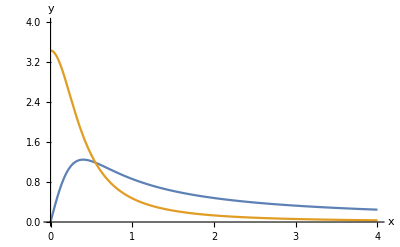

```mathematica
a=0.16;
b=0.55;
Plot[{x/(a+x^2),b/(a+x^2)},{x,0,4},PlotRange->{{0,4},{0,4}},AxesLabel->{x,y}]
```

Las ceroclinas nos ayudan a construir una región atrapante, chequemos esta región con el campo vectorial:

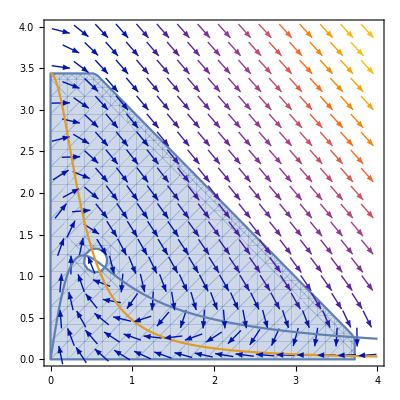

```mathematica
Show[{RegionPlot[(y<b/a)&& (y>0) && (x>0) && (y<-x+b*(1+1/a))&&(x<3.722)&&((x-b)^2+(y-b/(a+b^2))^2>0.02),{x,0,4},{y,0,4}],VectorPlot[{-x+a*y+y*x^2,b-a*y-y*x^2},{x,0,4},{y,0,4}],Plot[{x/(0.16+x^2),0.55/(0.16+x^2)},{x,0,4},PlotRange->{{0,4},{0,4}},AxesLabel->{x,y}]}]
```

Sólo basta que el punto de equilibrio sea repulsor para que las soluciones siempre salgan entren desde el círculo interior. Encontramos la matriz Jacobiana del sistema:

```mathematica
Clear[a]
Clear[b]
J=({{D[-x+a*y+y*x^2,x], D[-x+a*y+y*x^2,y]}, {D[b-a*y-y*x^2,x], D[b-a*y-y*x^2,y]}})
```

{{-1+2 x y,a+x^2},{-2 x y,-a-x^2}}

```mathematica
MatrixForm[J]
```

(-1+2 x y | a+x^2
-2 x y | -a-x^2)

y la evaluamos en el putno de equilibrio:

```mathematica
FullSimplify[MatrixForm[J/.{x->b,y->b/(a+b^2)}]]
```

(1-(2 a)/(a+b^2) | a+b^2
-(2 b^2)/(a+b^2) | -a-b^2)

La matriz tiene determinante:

```mathematica
FullSimplify[Det[J/.{x->b,y->b/(a+b^2)}]]
```

a+b^2

el cual siempre es positivo para , y traza:

```mathematica
FullSimplify[Tr[J/.{x->b,y->b/(a+b^2)}]]
```

1-b^2+a (-1-2/(a+b^2))

Esta expresión es difícil, pero podemos evaluar numéricamente cuando la traza es positiva y, por lo tanto, el punto de equilibrio es repulsor, y se cumple el teorema de Poincaré-Bendixson:

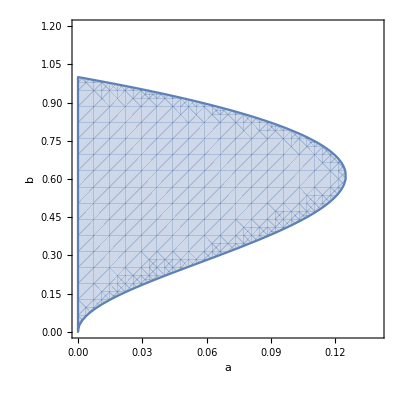

```mathematica
RegionPlot[Tr[J/.{x->b,y->b/(a+b^2)}]>0,{a,0,0.14},{b,0,1.2},FrameLabel->{a,b}]
```

Verificamos que exista un ciclo límite dentro de esta región:

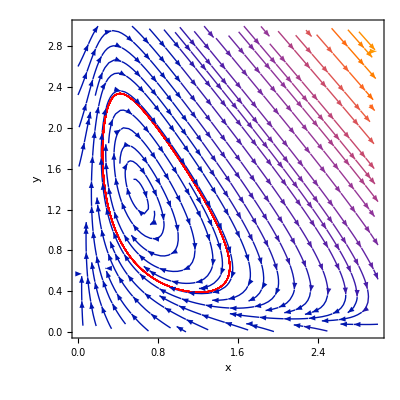

```mathematica
a=0.08;
b=0.6;
solcyc=NDSolve[{x'[t]==-x[t]+a*y[t]+y[t]*x[t]^2,y'[t]==b-a*y[t]-y[t]*x[t]^2,x[0]==1,y[0]==1},{x,y},{t,0,500}];
Show[{StreamPlot[{-x+a*y+y*x^2,b-a*y-y*x^2},{x,0,3},{y,0,3},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.solcyc],{t,400,500},PlotStyle->{Red,Thick}]}]
```

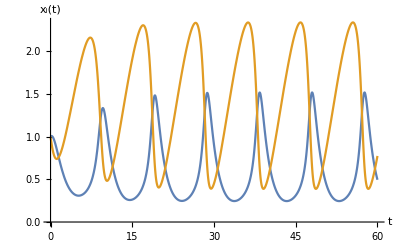

```mathematica
Plot[Evaluate[{x[t],y[t]}/.solcyc],{t,0,60},AxesLabel->{t,Subscript[x,i][t]}]
```